# Space Debris (Model H); color scheme : -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["Space-Debris-Model.nb",InsertResults->False];
myThickness=0.005;tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
```

## global parameters

```mathematica
(***   b , sL , sR , betL , betR , tauL , tauR : benefit parameters                      ***)
(***   a , tauC , betC , sC                    : cost parameters                         ***)
(***   Ts                                      : s-time-scale parameter                  ***)
(***   rlim , λ , inov , α (efficiency)        : Ṡ parameters (λ is dummy)               ***)
eps=1.0*10^-15;
rLIM =0.155; iNOV=0.845; α = 1.75; tLIM=360;
nGRID=100;dGRID=0.01;intervalWIDTH=40;pGOAL=40;
```

## FIG-04

dfig4/color-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     26.09

percentage of configs with 2     :     26.42

percentage of configs with 3     :     46.66

percentage of configs with 4     :     0.83

percentage of configs with s = 0 :     52.50

percentage of configs with s = 1 :     47.50

dfig4/color-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     25.97

percentage of configs with 2     :     0.98

percentage of configs with 3     :     0.01

percentage of configs with 4     :     73.04

percentage of configs with s = 0 :     26.95

percentage of configs with s = 1 :     73.05

dfig4/color-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     33.14

percentage of configs with 2     :     32.59

percentage of configs with 3     :     33.43

percentage of configs with 4     :     0.83

percentage of configs with s = 0 :     65.74

percentage of configs with s = 1 :     34.26

dfig4/color-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     55.32

percentage of configs with 2     :     0.98

percentage of configs with 3     :     0.01

percentage of configs with 4     :     43.69

percentage of configs with s = 0 :     56.30

percentage of configs with s = 1 :     43.70

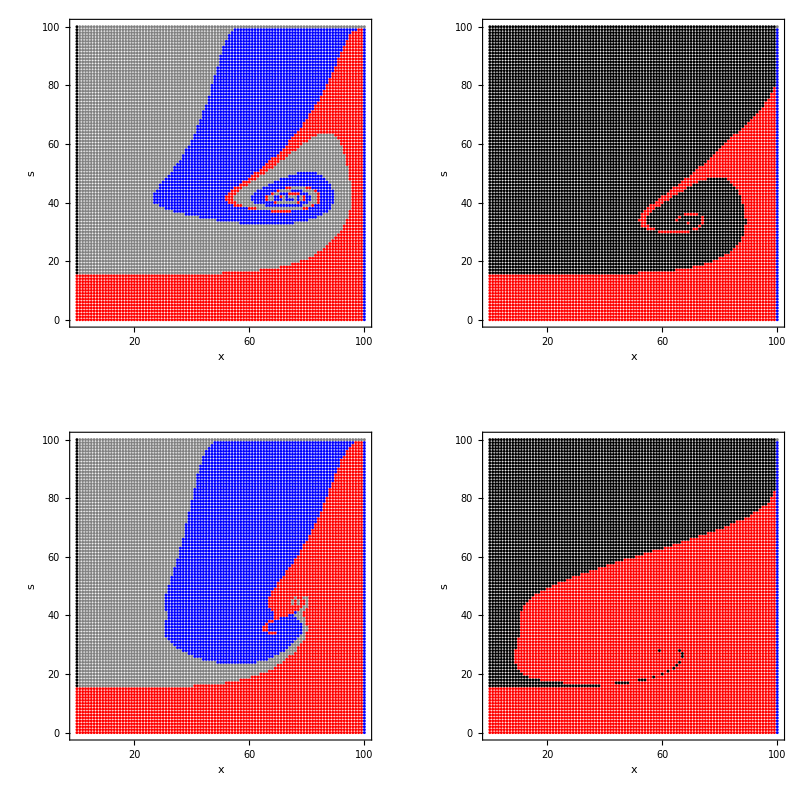

```mathematica
filname="dfig4/color-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl11=PlotGRID[nGRID,filname];
filname="dfig4/color-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl12=PlotGRID[nGRID,filname];
filname="dfig4/color-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl21=PlotGRID[nGRID,filname];
filname="dfig4/color-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl22=PlotGRID[nGRID,filname];
GraphicsGrid[{{pl11, pl12}, {pl21,pl22}},ImageSize->800]
```